```mathematica
tdata={7,14,28,90,180};
carQ1={16.8163475,3.43142355,0.46515,0.0116823,0.00379764};
carQ2={31.55036408,9.05121,2.12625,0.1123343,0.10444368};
carQ3={58.84667075,35.7016615,4.74985989,0.431325,0.40064941};
alc=10^3{0.16,0.28,0.48,0.49,0.47};
```

```mathematica
plotQuartile[mylist_?ListQ,c_,marker_]:=ListLogPlot[{tdata[[#]],mylist[[#]]}&/@Range[Length[tdata]],
Frame->True,
Axes->False,
PlotStyle->c,
PlotLegends->Automatic,
PlotMarkers->{marker,16},
PlotRange->All,
FrameLabel->{"Days post-infusion","CAR T (cells/µL)"},
FrameStyle->Directive[Thickness[0.0035],Black],
LabelStyle->{FontSize->18,Black,FontFamily->"Arial"},
ImageSize->500];
```

```mathematica
{n,c,b}=.;
```

```mathematica
n0=6.0;c0=0.36;b0=94.86;T=200;kN=500.0;rB=0.065;
```

```mathematica
(*Models*)
modelNoALCNoTumor[rN_,rC_,kC_,k2_,γB_]:=
NDSolve[{
n'[t]==-rN n[t]Log[(n[t]+c[t])/kN],
c'[t]==-rC c[t]Log[(n[t]+c[t])/kC],
b'[t]==rB b[t]-γB b[t] (k2 c[t])/(1+k2 c[t]),
n[0]==n0,c[0]==c0,b[0]==b0},
{n,c,b},{t,T},
PrecisionGoal->20];
modelNoALCTumor[rN_,rC_,kC_,k1_,k2_,rC0_,γB_]:=
NDSolve[{
n'[t]==-rN n[t]Log[(n[t]+c[t])/kN],
c'[t]==-(rC0+(rC k1 b[t])/(1+k1 b[t]))c[t]Log[(n[t]+c[t])/kC],
b'[t]==rB b[t]-γB b[t] (k2 c[t])/(1+k2 c[t]),
n[0]==n0,c[0]==c0,b[0]==b0},
{n,c,b},{t,T},
PrecisionGoal->20];
modelALCNoTumor[rN_,rC_,kC_,k2_,a1_,a2_,γB_]:=
NDSolve[{
n'[t]==-rN n[t]Log[(n[t]+c[t])/kN],
c'[t]==-(rC+(a2 (n[t]+c[t]-kN)^2)/((n[t]+c[t]-kN)^2+a1(n[t]+c[t])^2))c[t]Log[(n[t]+c[t])/kC],
b'[t]==rB b[t]-γB b[t] (k2 c[t])/(1+k2 c[t]),
n[0]==n0,c[0]==c0,b[0]==b0},
{n,c,b},{t,T},
PrecisionGoal->20];
modelALCTumor[rN_,rC_,kC_,k1_,k2_,a1_,a2_,γB_]:=
NDSolve[{
n'[t]==-rN n[t]Log[(n[t]+c[t])/kN],
c'[t]==-((rC k1 b[t])/(1+k1 b[t])+(a2 (n[t]+c[t]-kN)^2)/((n[t]+c[t]-kN)^2+a1(n[t]+c[t])^2))c[t]Log[(n[t]+c[t])/kC],
b'[t]==rB b[t]-γB b[t] (k2 c[t])/(1+k2 c[t]),
n[0]==n0,c[0]==c0,b[0]==b0},
{n,c,b},{t,T},
PrecisionGoal->20];
```

```mathematica
(*Data*)
noALCNoTumorData=Import[NotebookDirectory[]<>"outputData_noTumor_noALC_dependence_params_1_2020-09-24.txt","Data"];
noALCTumorData=Import[NotebookDirectory[]<>"outputData_Tumor_noALC_dependence_params_1_2020-09-24.txt","Data"];
ALCNoTumorData=Import[NotebookDirectory[]<>"outputData_noTumor_ALC_dependence_params_1_2020-09-24.txt","Data"];
ALCTumorData=Import[NotebookDirectory[]<>"outputData_Tumor_ALC_dependence_params_1_2020-09-24.txt","Data"];
```

```mathematica
(* Solve models with obtained fitted parameters *)
modelFitNoALCNoTumor=Flatten[modelNoALCNoTumor@@noALCNoTumorData[[#]]&/@Range[2,4],1];
modelFitNoALCTumor=Flatten[modelNoALCTumor@@noALCTumorData[[#]]&/@Range[2,4],1];
modelFitALCNoTumor=Flatten[modelALCNoTumor@@ALCNoTumorData[[#]]&/@Range[2,4],1];
modelFitALCTumor=Flatten[modelALCTumor@@ALCTumorData[[#]]&/@Range[2,4],1];
```

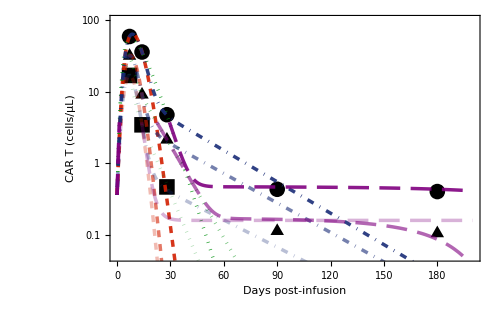

```mathematica
(* Plot quartile and model fits *)
Show[plotQuartile[carQ1,Black,"■"],plotQuartile[carQ2,Black,"▲"],plotQuartile[carQ3,Black,"●"],LogPlot[Evaluate[c[t]/.modelFitNoALCNoTumor],{t,0,T},
PlotStyle->Flatten[{Directive[ColorData["SolarColors"][0.25],Dashed,Thickness[0.005],Opacity[#]]&/@{0.3,0.6,0.9}},1]
],
LogPlot[Evaluate[c[t]/.modelFitNoALCTumor],{t,0,T},
PlotStyle->Flatten[{Directive[ColorData["GreenPinkTones"][0.1],Dotted,Thickness[0.005],Opacity[#]]&/@{0.3,0.6,0.9}},1]
],
LogPlot[Evaluate[c[t]/.modelFitALCNoTumor],{t,0,T},
PlotStyle->Flatten[{Directive[ColorData["BlueGreenYellow"][0.1],DotDashed,Thickness[0.005],Opacity[#]]&/@{0.3,0.6,0.9}},1]
],
LogPlot[Evaluate[c[t]/.modelFitALCTumor],{t,0,T},
PlotStyle->Flatten[{Directive[Purple,Dashing[{0.03,0.015}],Thickness[0.005],Opacity[#]]&/@{0.3,0.6,0.9}},1]
],
PlotRange->{All,{-3,4.6}}]
```

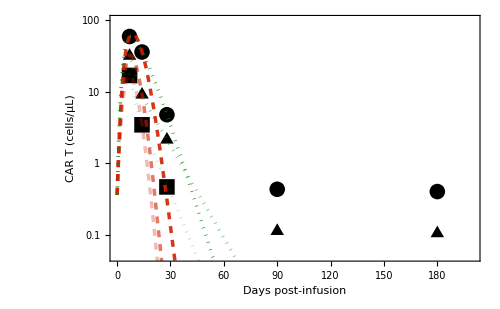

```mathematica
Show[plotQuartile[carQ1,Black,"■"],plotQuartile[carQ2,Black,"▲"],plotQuartile[carQ3,Black,"●"],LogPlot[Evaluate[c[t]/.modelFitNoALCNoTumor],{t,0,T},
PlotStyle->Flatten[{Directive[ColorData["SolarColors"][0.25],Dashed,Thickness[0.005],Opacity[#]]&/@{0.3,0.6,0.9}},1],
PlotLegends->Placed[{" "," "," "},{0.45,0.8}]
],
LogPlot[Evaluate[c[t]/.modelFitNoALCTumor],{t,0,T},
PlotStyle->Flatten[{Directive[ColorData["GreenPinkTones"][0.1],Dotted,Thickness[0.005],Opacity[#]]&/@{0.3,0.6,0.9}},1],
PlotLegends->Placed[{" "," "," "},{0.75,0.8}]
],
PlotRange->{All,{-3,4.6}}]
```

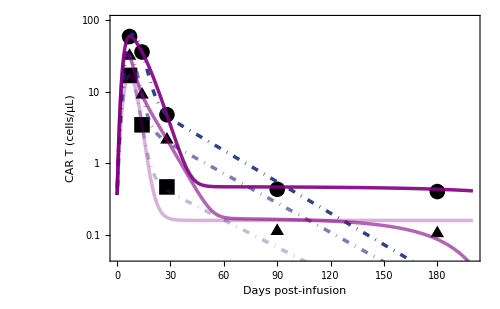

```mathematica
Show[plotQuartile[carQ1,Black,"■"],plotQuartile[carQ2,Black,"▲"],plotQuartile[carQ3,Black,"●"],
LogPlot[Evaluate[c[t]/.modelFitALCNoTumor],{t,0,T},
PlotStyle->Flatten[{Directive[ColorData["BlueGreenYellow"][0.1],DotDashed,Thickness[0.005],Opacity[#]]&/@{0.3,0.6,0.9}},1],
PlotLegends->Placed[{" "," "," "},{0.45,0.8}]
],
LogPlot[Evaluate[c[t]/.modelFitALCTumor],{t,0,T},
PlotStyle->Flatten[{Directive[Purple,Thickness[0.005],Opacity[#]]&/@{0.3,0.6,0.9}},1],
PlotRange->All,
PlotLegends->Placed[{" "," "," "},{0.75,0.8}]
],
PlotRange->{All,{-3,4.6}}]
```

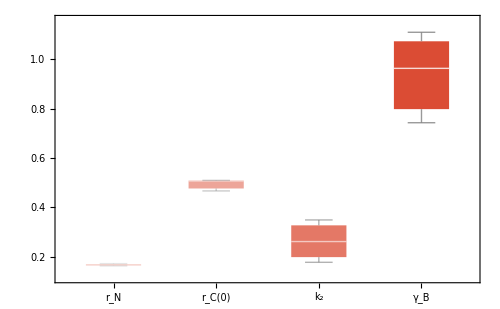

```mathematica
BoxWhiskerChart[Transpose@noALCNoTumorData[[2;;,{1,2,4,5}]],
ChartStyle->{Directive[ColorData["SolarColors"][0.25],Opacity[#/Length[noALCNoTumorData[[2]]]]]&/@Range[Length[noALCNoTumorData[[2]]]]},
ChartLabels->{"r_N","r_C(0)","k_2","γ_B"},
FrameStyle->Directive[Thickness[0.0025],Black],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
ImageSize->500
]
```

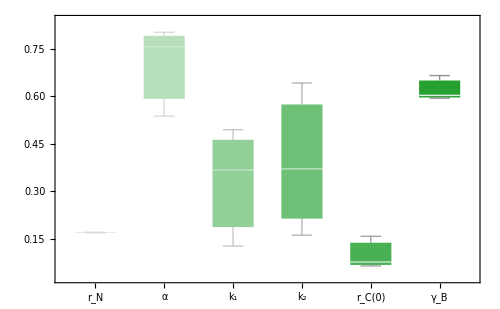

```mathematica
BoxWhiskerChart[Transpose@noALCTumorData[[2;;,{1,2,4,5,6,7}]],
ChartStyle->{Directive[ColorData["GreenPinkTones"][0.1],Opacity[#/Length[noALCTumorData[[2]]]]]&/@Range[Length[noALCTumorData[[2]]]]},
ChartLabels->{"r_N","α","k_1","k_2","r_C(0)","γ_B"},
FrameStyle->Directive[Thickness[0.0025],Black],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
ImageSize->500
]
```

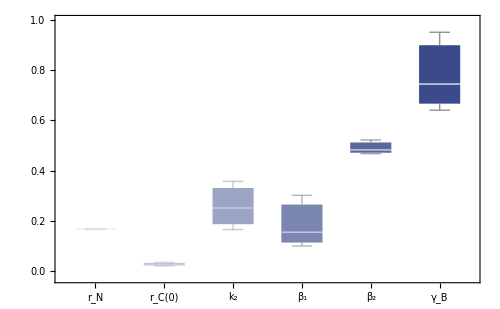

```mathematica
BoxWhiskerChart[Transpose@ALCNoTumorData[[2;;,{1,2,4,5,6,7}]],
ChartStyle->{Directive[ColorData["BlueGreenYellow"][0.1],Opacity[#/Length[ALCNoTumorData[[2]]]]]&/@Range[Length[ALCNoTumorData[[2]]]]},
ChartLabels->{"r_N","r_C(0)","k_2","β_1","β_2","γ_B"},
FrameStyle->Directive[Thickness[0.0025],Black],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
ImageSize->500
]
```

```mathematica
ALCNoTumorData[[1]]
```

{#rN,,rC,,kC,,k2,,a,,b,,gammaB}

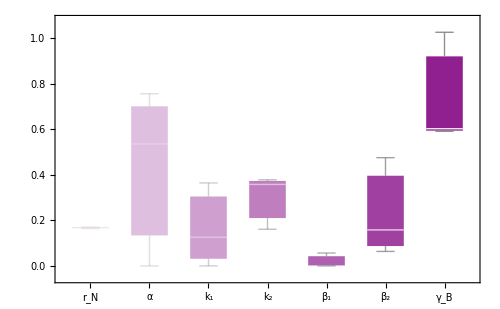

```mathematica
BoxWhiskerChart[Transpose@ALCTumorData[[2;;,{1,2,4,5,6,7,8}]],
ChartStyle->{Directive[Purple,Opacity[#/Length[ALCTumorData[[2]]]]]&/@Range[Length[ALCTumorData[[2]]]]},
ChartLabels->{"r_N","α","k_1","k_2","β_1","β_2","γ_B"},
FrameStyle->Directive[Thickness[0.0025],Black],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
ImageSize->500
]
```

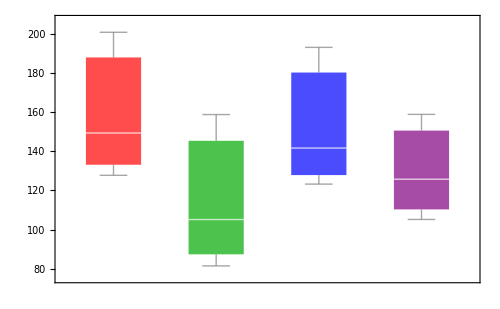

```mathematica
BoxWhiskerChart[{noALCNoTumorData[[2;;,3]],noALCTumorData[[2;;,3]],ALCNoTumorData[[2;;,3]],ALCTumorData[[2;;,3]]},
ChartStyle->mycolor,
FrameStyle->Directive[Thickness[0.0025],Black],
LabelStyle->{Black,FontSize->18,FontFamily->"Arial"},
ImageSize->500
]
```

```mathematica
noALCNoTumorData[[1]]
noALCTumorData[[1]]
ALCNoTumorData[[1]]
ALCTumorData[[1]]
```

{#rN,,rC,,kC,,k2,,gammaB}

{#rN,,rC,,kC,,k1,,k2,,rC0,,gammaB}

{#rN,,rC,,kC,,k2,,a,,b,,gammaB}

{#rN,,rC,,kC,,k1,,k2,,a,,b,,gammaB}

```mathematica
color={Red,Darker[Green],Blue,Purple}
```

{RGBColor[1, 0, 0],RGBColor[0, Rational[2, 3], 0],RGBColor[0, 0, 1],RGBColor[0.5, 0, 0.5]}

```mathematica
mycolor=Directive[{color[[#]],Opacity[0.7]}]&/@Range[4]
```

{Directive[{RGBColor[1, 0, 0],Opacity[0.7]}],Directive[{RGBColor[0, Rational[2, 3], 0],Opacity[0.7]}],Directive[{RGBColor[0, 0, 1],Opacity[0.7]}],Directive[{RGBColor[0.5, 0, 0.5],Opacity[0.7]}]}

```mathematica
(* BIC *)
n=11;k={5,5,5,7,7,7,7,7,7,8,8,8};
bic=n Log[Total[1/Max[carQ1]^2(Flatten[c[#]&/@tdata/.{modelFitNoALCNoTumor,modelFitNoALCTumor,modelFitALCNoTumor,modelFitALCTumor},1]-ConstantArray[carQ1,12])^2+1/Max[alc-carQ1]^2(Flatten[n[#]&/@tdata/.{modelFitNoALCNoTumor,modelFitNoALCTumor,modelFitALCNoTumor,modelFitALCTumor},1]-ConstantArray[alc-carQ1,12])^2,{2}]]-n Log[n]+(k+1)Log[n];
bic[[1;;;;3]]
bic[[2;;;;3]]
bic[[3;;;;3]]
```

{-60.9014,-55.2057,-56.6158,-53.9792}

{-13.2535,-8.32755,-8.35049,-5.92882}

{13.2994,18.1627,18.1494,20.562}

```mathematica
(* AIC *)
dataPts=11;k={5,5,5,7,7,7,7,7,7,8,8,8};
aic=dataPts Log[Total[1/Max[carQ1]^2(Flatten[c[#]&/@tdata/.{modelFitNoALCNoTumor,modelFitNoALCTumor,modelFitALCNoTumor,modelFitALCTumor},1]-ConstantArray[carQ1,12])^2+1/Max[alc-carQ1]^2(Flatten[n[#]&/@tdata/.{modelFitNoALCNoTumor,modelFitNoALCTumor,modelFitALCNoTumor,modelFitALCTumor},1]-ConstantArray[alc-carQ1,12])^2,{2}]]-dataPts Log[dataPts]+(k+1)2;
aic[[1;;;;3]]
aic[[2;;;;3]]
aic[[3;;;;3]]
```

{-63.2888,-58.3888,-59.7989,-57.5602}

{-15.6408,-11.5107,-11.5336,-9.50988}

{10.912,14.9795,14.9662,16.9809}

```mathematica
aicLogLoss=n Log[Total[Log[(Flatten[Abs[c[#]]&/@tdata/.{modelFitNoALCNoTumor,modelFitNoALCTumor,modelFitALCNoTumor,modelFitALCTumor},1]/ConstantArray[carQ1,12])]^2+Log[(Flatten[Abs[n[#]]&/@tdata/.{modelFitNoALCNoTumor,modelFitNoALCTumor,modelFitALCNoTumor,modelFitALCTumor},1]/ConstantArray[alc-carQ1,12])]^2,{2}]]-n Log[n]+(k+1)2+((k+1)2(k+2))/(n-1-(k+1));
aicLogLoss[[1;;;;3]]
aicLogLoss[[2;;;;3]]
aicLogLoss[[3;;;;3]]
```

{80.2288,126.648,74.3841,205.505}

{80.2663,125.172,91.9021,204.868}

{79.1258,123.169,99.442,214.339}

```mathematica
modelLikelihoods=Exp[(Min[aic[[1;;;;3]]]-aic[[1;;;;3]])/2];
```

```mathematica
modelLikelihoods/Total[modelLikelihoods]
```

{0.758735,0.0654768,0.132521,0.0432672}

```mathematica
modelLikelihoods
```

{1.,0.0862973,0.17466,0.0570255}

```mathematica
ALCNoTumorData
```

{{#rN,,rC,,kC,,k2,,a,,b,,gammaB},{0.164722,0.0208421,123.264,0.357296,0.154976,0.46749,0.950376},{0.16952,0.025069,141.656,0.251229,0.301621,0.521804,0.744344},{0.169555,0.0354003,193.029,0.165377,0.0999665,0.482325,0.640354}}